```mathematica
Unprotect[TbarFunction,Simplify,Inverse,NonCommutativeMultiply,Equal,Unequal,Power,ShowGraph,RationalToString,Commutator,idTbar];
FullPointList[f_TbarFunction]:=Join[List@@f,{First@f+{1,1}}]
IsCollinear[{pt1_,pt2_,pt3_}]:=(Divide@@(pt3-pt2)==Divide@@(pt2-pt1))
Simplify[f_TbarFunction]:=With[{pts=FullPointList[f]},
TbarFunction@@Join[{First@pts},pts⟦Select[Range[2,Length[pts]-1],!IsCollinear[pts⟦#-1;;#+1⟧]&]⟧]]
Inverse[f_TbarFunction]:=Simplify@With[{pts=Sort@Table[{pt⟦2⟧,pt⟦1⟧}-Floor[pt⟦2⟧]*{1,1},{pt,List@@f}]},
TbarFunction@@If[pts⟦1,1⟧==0,pts,Join[{{0,-1+pts⟦-1,2⟧+(1-pts⟦-1,1⟧)/(1+pts⟦1,1⟧-pts⟦-1,1⟧)(pts⟦1,2⟧-pts⟦-1,2⟧+1)}},pts]]]
NonCommutativeMultiply[f_TbarFunction,g_TbarFunction]:=With[{G=Inverse[g]},
With[{xbreaks=Union[First/@(List@@g),Mod[#,1]&/@(G/@(First/@(List@@f)))]},
Simplify[TbarFunction@@Table[{x,f[g[x]]},{x,xbreaks}]]
]]
Power[f_TbarFunction,n_Integer]:=Which[
n<0,Inverse[f]^(-n),
n==0,TbarFunction[{0,0}],
n==1,f,
True,NonCommutativeMultiply@@ConstantArray[f,n]
]
Power[f_TbarFunction,g_TbarFunction]:=Inverse[g]**f**g
Equal[f1_TbarFunction,f2_TbarFunction]:=(f1===f2)
f_TbarFunction[x_?NumberQ]:=With[{pts=FullPointList[f]},
With[{k=SelectFirst[Range@Length@pts,pts⟦#+1,1⟧≥Mod[x,1]&]},Floor[x]+pts⟦k,2⟧+((Mod[x,1]-pts⟦k,1⟧)(pts⟦k+1,2⟧-pts⟦k,2⟧))/(pts⟦k+1,1⟧-pts⟦k,1⟧)]]
Unequal[f1_TbarFunction,f2_TbarFunction]:=!(f1==f2)
RationalToString[p_]:=If[Denominator[p]==1,ToString[Numerator[p]],ToString[Numerator@p]<>"/"<>ToString[Denominator[p]]]
ShowGraph[f_TbarFunction]:=With[{pts=FullPointList@f},
Graphics[{AbsolutePointSize[5],
Table[Tooltip[Line[{pts⟦k⟧,pts⟦k+1⟧}],"slope "<>ToString[1/Divide@@(pts⟦k+1⟧-pts⟦k⟧),InputForm]],{k,1,Length[pts]-1}],
Table[Tooltip[Point[p],"("<>ToString[p⟦1⟧,InputForm]<>", "<>ToString[p⟦2⟧,InputForm]<>")"],{p,pts}]},Frame->True,FrameStyle->Thick,PlotRange->{{0,1},{f[0],f[1]}},GridLines->{Range[1,7]/8,Range[Floor[8f[0]]+1,Ceiling[8f[1]]-1]/8},
FrameTicks->{{0,{1/4,"1/4"},{1/2,"1/2"},{3/4,"3/4"},1},
Table[{y,RationalToString[y]},{y,Range[Floor[4f[0]]+1,Ceiling[4f[1]]-1]/4}]
,{},{}},FrameTicksStyle->12]]
Commutator[f_TbarFunction,g_TbarFunction]:=f**g**Inverse[f]**Inverse[g]
idTbar=TbarFunction[{0,0}];
Protect[TbarFunction,Simplify,Inverse,NonCommutativeMultiply,Equal,Unequal,Power,ShowGraph,RationalToString,Commutator,idTbar];
```

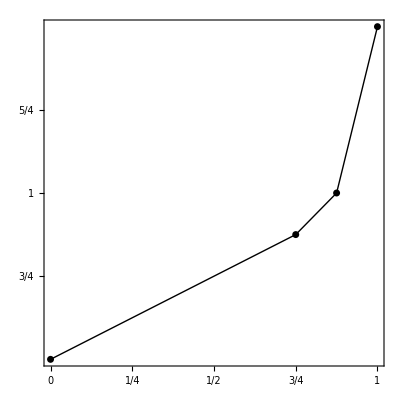
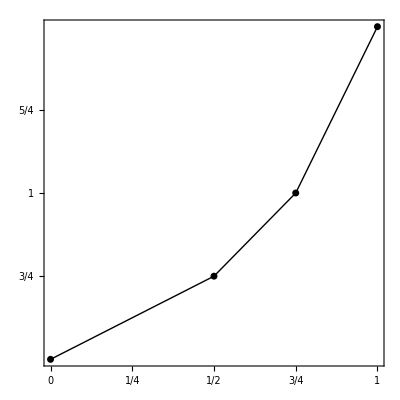

```mathematica
a=TbarFunction[{0,1/2},{3/4,7/8},{7/8,1}];
b=TbarFunction[{0,1/2},{1/2,3/4},{3/4,1}];
ShowGraph/@{a,b}
```

```mathematica
a^4==b^3
(b**a)^5==b^9
Commutator[b**a**b,a^2**b**a**b**a^2]==TbarFunction[{0,0}]
Commutator[b**a**b,a^2**b^2**a^2**b**a**b**a^2**b**a^2]==TbarFunction[{0,0}]
```

True

True

True

«1 more identical outputs»

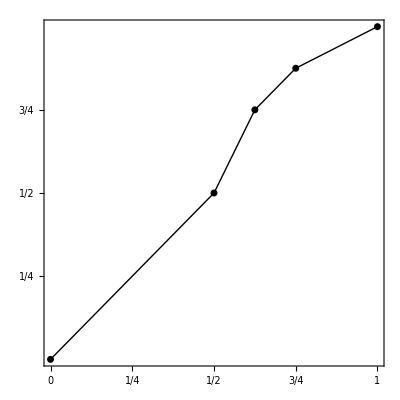
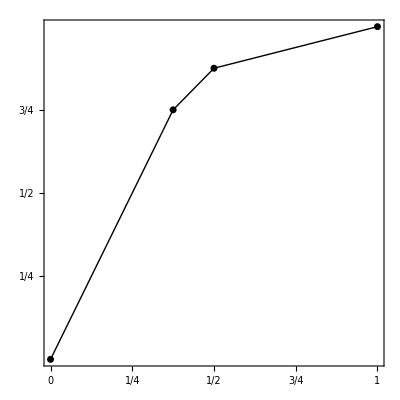
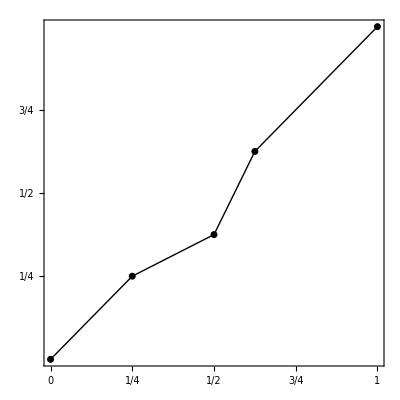

```mathematica
p=a^(-1)**b;
q=a^(-1)**b**a^2**b^(-1);
r=b^(-1)**a**b**a^2**(a**b)^(-2)**b**a^(-1)**b;
ShowGraph/@{p,q,r}
```

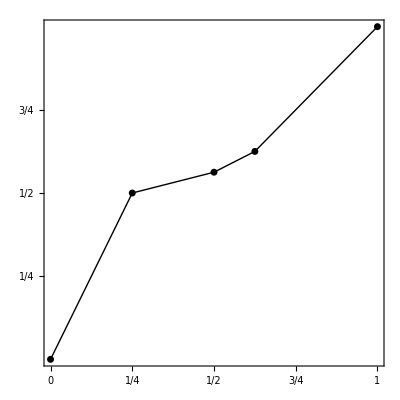
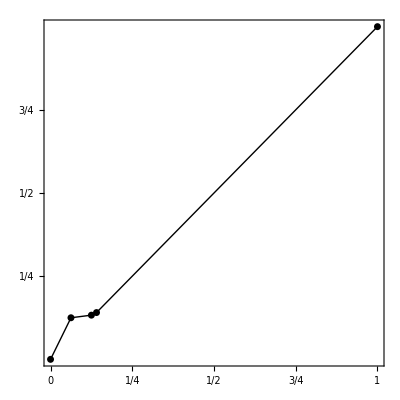
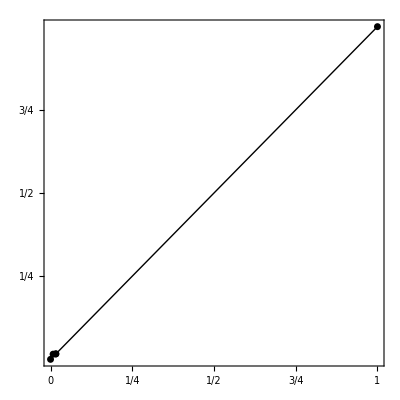

```mathematica
t[3]=b^2**a**(a**b)^(-2)**b;
t[n_]:=t[n]=(t[n-1]^(q^(n-2)))**(r^(p^(n-4)**q^(n(n-3)/2)))
ShowGraph/@{t[3],t[4],t[5]}
```

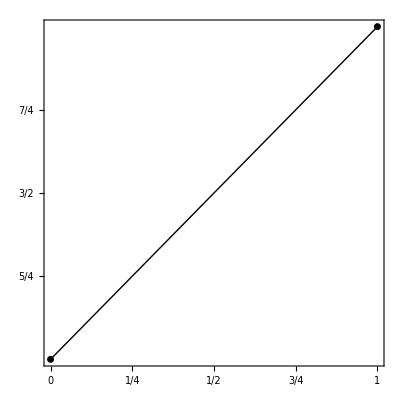
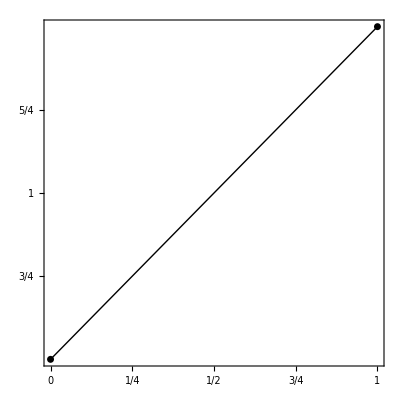
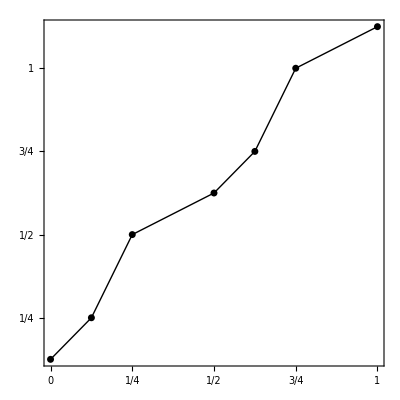

```mathematica
s[1]=b^3;
s[2]=b**a^2**b^(-1);
s[3]=b^(-1)**a**b**a^(-2)**b**a**b**a^(-1)**b^(-1);
ShowGraph/@{s[1],s[2],s[3]}
```

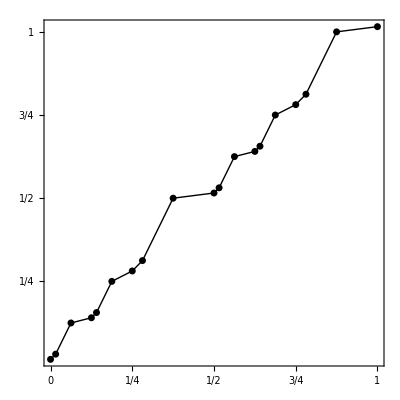
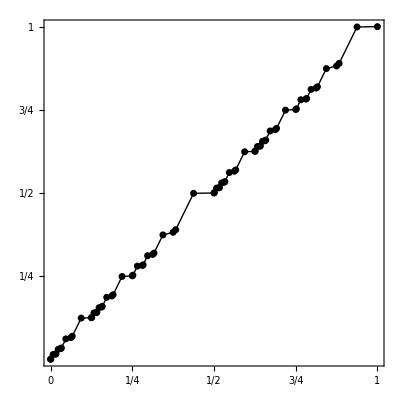
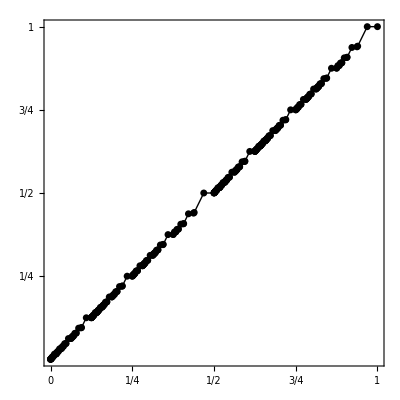

```mathematica
s[n_]:=s[n]=Commutator[t[n],t[n]^s[n-1]]**s[1]**(s[n-1]^(-1)**t[n])^((n-1)!)
ShowGraph/@{s[4],s[5],s[6]}
```

```mathematica
Table[s[n]^n==s[n-1],{n,2,6}]
```

{True,True,True,True,True}

```mathematica
d[1]=1;
d[n_]:=d[n]=d[n-1]/2^(n-1)
Table[
{{0,d[n]},{d[n],2d[n]},{d[n-1]/2,d[n-1]}}==(List@@s[n])[[1;;3]],{n,3,6}]
```

{True,True,True,True}